Метод Ньютона-Рафсона (касательных) 2.1.4

Дано: 
f (x) -  дифференцируемая функция,  
x0 - начальное приближение, 
k - количество итераций

```mathematica
Clear@newtonsMethodIter
```

```mathematica
newtonsMethodIter[f_,x0_,k_]:= 
Module[
{acc = 0.0001,x1 = x0 - f[x0]/ND[f[x],x,x0]},
Do[x1=x1- f[x1]/ND[f[x],x,x1], {n,1 ,k}];
x1]
```

Результат работы алгоритма

Пример 1

```mathematica
Clear@f
```

```mathematica
f[x_]:= x^2-1;
x0= -5;
k = 4;
```

```mathematica
newtonsMethodIter[f,x0,k]
```

-1.

Проверка 1

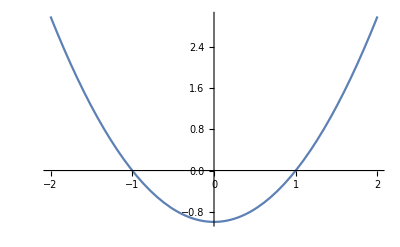

```mathematica
Plot[f[x],{x,-2,2}]
```

Пример 2

```mathematica
f[x_]:= ⅇ^x-5;
x0= 5;
k = 25;
```

```mathematica
newtonsMethodIter[f,x0,k]
```

1.60944

Проверка 2

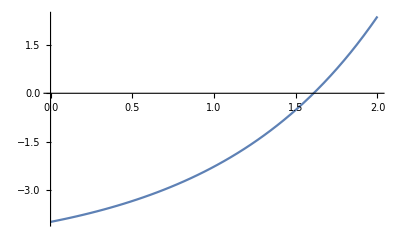

```mathematica
Plot[ⅇ^x-5,{x,0,2}]
```

```mathematica
Log[5.]//Simplify
```

1.60944